```mathematica
(* define position vector as a function of x *)
r[x_,y_,z_]:={x,y,z};
(* define magnetic moment μ *)
m:={0,0,μ};
(* test *)
m.r[x,y,z]
(* physical constant *)
pars={μ0-> 4*π*1*^-7,μ->8.8};
```

z μ

```mathematica
(* define dipole field as a function of r vector *)
B[r_]:=(μ0/(4*π))((3r(m.r))/Norm[r]^5-m/Norm[r]^3)
```

```mathematica
(* calculate the dBz/dx assuming one centimeter offset in z *)
D[B[r[x,y,z]], x]/.y->0/.z->0.1
```

{(0.0238732 μ μ0)/((0.01+Abs[x]^2)^(5/2))-(0.119366 x μ μ0 Abs[x] Abs'[x])/((0.01+Abs[x]^2)^(7/2)),0,(μ0 (-(0.15 μ Abs[x] Abs'[x])/((0.01+Abs[x]^2)^(7/2))+(3 μ Abs[x] Abs'[x])/((0.01+Abs[x]^2)^(5/2))))/(4 π)}

```mathematica
(* define derivative using assumption to get rid of derivatives of absolute value *)
dBdx=FullSimplify[D[B[r[x,y,z]], x]/.y->0/.z->0.1,Assumptions->{Element[x,Reals]}]
```

{((0.000238732-0.095493 x^2) μ μ0)/((0.01+x^2)^(7/2)),0,(x (-0.0095493+0.238732 x^2) μ μ0)/((0.01+x^2)^(7/2))}

```mathematica
(* estimate typical values of dBdx *)
dBdx/.pars/.x->1*^-18
```

{0.0264,0,-1.056×10^-18}

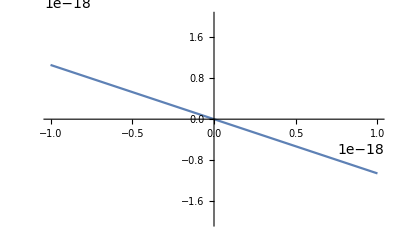

```mathematica
(* plot results *)
Plot[
dBdx[[3]]/.pars,
{x,-1*^-18,1*^-18},
PlotRange->{-2*^-18,2*^-18}
]
```

```mathematica
(* define derivative using assumption to get rid of derivatives of absolute value *)
dBdz=FullSimplify[D[B[r[x,y,z]], z]/.x->0/.y->0,Assumptions->{Element[z,Reals]}]
```

{0,0,-(3 μ μ0 Abs[z])/(2 π z^5)}

```mathematica
(* estimate typical values of dBdz *)
dBdz/.pars/.z->0.01
```

{0,0,-528.}